```mathematica
ff[s_,a_] := (1-a^(1-s))Zeta[s]
```

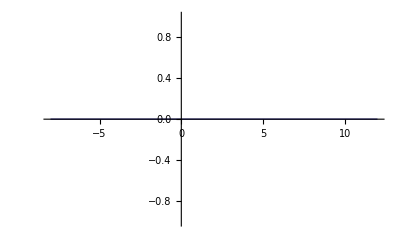

```mathematica
Plot[ Abs[ff[-4,k]],{k,-8,12}]
```

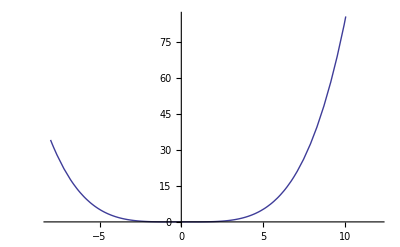

```mathematica
Plot[ Abs[ff[-3,k]],{k,-8,12}]
```

```mathematica
Plot[ Abs[ff[-2,k]],{k,-8,12}]
```

-Graphics-

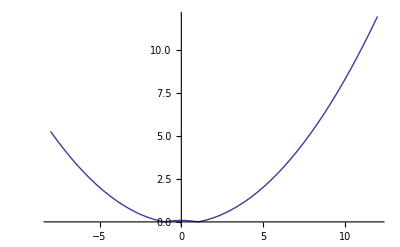

```mathematica
Plot[ Abs[ff[-1,k]],{k,-8,12}]
```

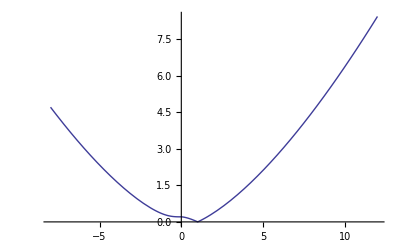

```mathematica
Plot[ Abs[ff[-1/2,k]],{k,-8,12}]
```

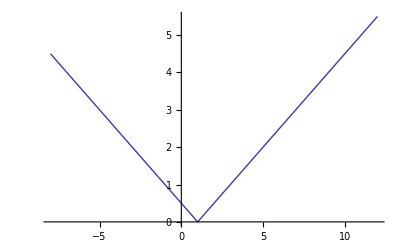

```mathematica
Plot[ Abs[ff[0,k]],{k,-8,12}]
```

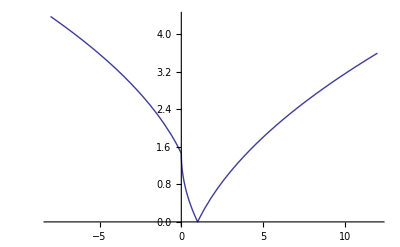

```mathematica
Plot[ Abs[ff[1/2,k]],{k,-8,12}]
```

```mathematica
Plot[ Abs[ff[1,k]],{k,-8,12}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics-

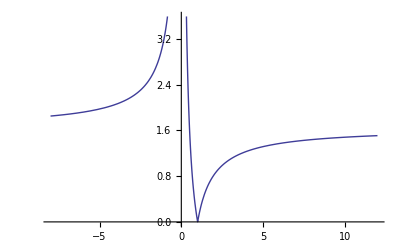

```mathematica
Plot[ Abs[ff[2,k]],{k,-8,12}]
```

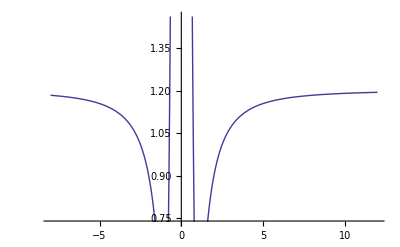

```mathematica
Plot[ Abs[ff[3,k]],{k,-8,12}]
```

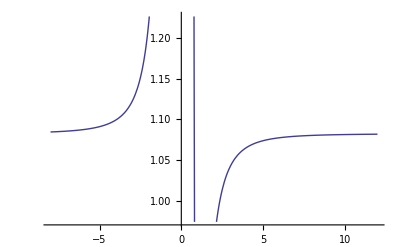

```mathematica
Plot[ Abs[ff[4,k]],{k,-8,12}]
```

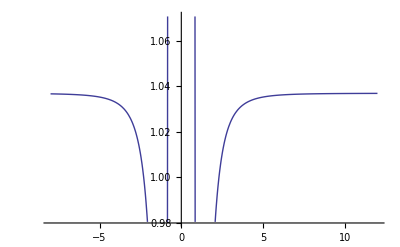

```mathematica
Plot[ Abs[ff[5,k]],{k,-8,12}]
```

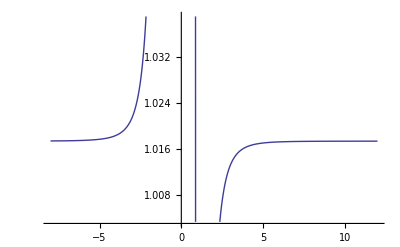

```mathematica
Plot[ Abs[ff[6,k]],{k,-8,12}]
```

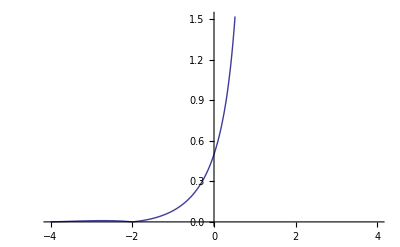

Power::infy: Infinite expression 1/0^3.1 encountered.

```mathematica
Plot[ Abs[ff[k,0]],{k,-4,4}]
```

```mathematica
Abs[ff[3.12,0]]
```

Power::infy: Infinite expression 1/0^2.12 encountered.

∞

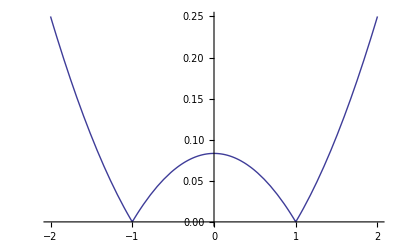

```mathematica
Plot[ Abs[ff[-1,k]],{k,-2,2}]
```

```mathematica
ff[-1/2,0]
```

Zeta[-1/2]

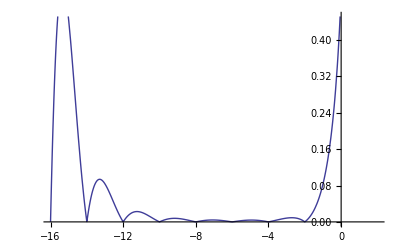

```mathematica
Plot[ Abs[ff[k,0]],{k,-16,2}]
```

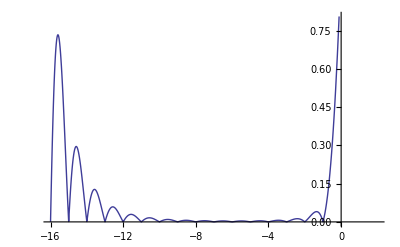

```mathematica
Plot[ Abs[ff[k,-1]],{k,-16,2}]
```

```mathematica
Plot[ Abs[ff[k,0]],{k,-16,2}]
```

-Graphics-

```mathematica
ff[1,2]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[ HarmonicNumber[(-1)x]-HarmonicNumber[x],{x->Infinity}]
```

{Interval[{-∞,∞}]}

```mathematica
Sum[ 1/(2n+1),{n,0,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=0)^∞ 1/(1+2 n)

```mathematica
Zeta[3.17]
```

1.17156

```mathematica
2^(3.17) Pi^(3.17-1) Sin[Pi 3.17/2] Gamma[1-3.17]Zeta[1-3.17]
```

1.17156

```mathematica
Zeta[1-3.17]
```

0.00429085

```mathematica
st[s_]:=2^(s) Pi^(s-1) Sin[Pi s/2] Gamma[1-s]Zeta[1-s]
```

```mathematica
st[2.3]
```

1.43242

```mathematica
Zeta[1-2.3]
```

-0.0434641

```mathematica
Zeta[2.3]
```

1.43242

```mathematica
2^(s) Pi^(s-1) Sin[Pi s/2] Gamma[1-s]Zeta[1-s] /.s->3.3
```

1.15194

```mathematica
Zeta[3.3]
```

1.15194

```mathematica
ff[3.3]
```

0.918027

```mathematica
zt[s_] := ff[s]/(1-2^(1-s))
```

```mathematica
zt[3.3]
```

1.15194

```mathematica
ff[s_] := (1-t^(1-s))Zeta[s] /. t->2
(2^(s) Pi^(s-1) Sin[Pi s/2] Gamma[1-s]ff[1-s]/(1-t^s)) /.{s->3.3,t->2}
ff[s]/(1-t^(1-s))/.{s->3.3,t->2}
```

1.15194

1.15194

```mathematica
ff[s_] := (1-t^(1-s))Zeta[s] /. t->2
(1-t^(1-s))(2^(s) Pi^(s-1) Sin[Pi s/2] Gamma[1-s]ff[1-s]/(1-t^s)) /.{s->3.3,t->2}
ff[s]/.{s->3.3}
```

0.918027

0.918027

```mathematica
ff[s_] := (1-t^(1-s))Zeta[s] /. t->3
(1-t^(1-s))(2^(s) Pi^(s-1) Sin[Pi s/2] Gamma[1-s]ff[1-s]/(1-t^s)) /.{s->4.3,t->3}
ff[s]/.{s->4.3}
```

1.03593

1.03593

```mathematica
gg[s_] := (1-t^(1-s))Zeta[s]
```

```mathematica
FullSimplify[(1-t^(1-s))(2^(s) Pi^(s-1) Sin[Pi s/2] Gamma[1-s]hh[1-s]/(1-t^s))]
```

(2^s π^(-1+s) (1-t^(1-s)) Gamma[1-s] hh[1-s] Sin[(π s)/2])/(1-t^s)

```mathematica
2^s π^(-1+s) (1-t^(1-s))/(1-t^s) Gamma[1-s] hh[1-s] Sin[(π s)/2]
```

(2^s π^(-1+s) (1-t^(1-s)) Gamma[1-s] hh[1-s] Sin[(π s)/2])/(1-t^s)

```mathematica
ff[s_] := (1-t^(1-s))Zeta[s] /. t->3
2^s π^(-1+s) (1-t^(1-s))/(1-t^s) Gamma[1-s] ff[1-s] Sin[(π s)/2]/.{s->3.1,t->3}
ff[s]/.{s->3.1}
```

1.06558

1.06558

```mathematica
ff[s_,t_] := (1-t^(1-s))Zeta[s]
f1[s_,t_]:=2^s π^(-1+s) (1-t^(1-s))/(1-t^s) Gamma[1-s] ff[1-s,t] Sin[(π s)/2]
```

```mathematica
N[ff[.5,-2]]
```

-1.46035+2.06525 ⅈ

```mathematica
N[f1[.5,-2]]
```

-1.46035+2.06525 ⅈ

```mathematica
N[f1[.5,-1]]
```

-1.46035+1.46035 ⅈ

```mathematica
N[f1[.5,-.5]]
```

-1.46035+1.03263 ⅈ

```mathematica
N[f1[.7,-.5]]
```

-1.4519+1.82575 ⅈ

```mathematica
N[f1[.7,-1]]
```

-1.14529+2.24776 ⅈ

```mathematica
Table[{k, N[ff[.5,k]]},{k,-2,2,.1}]//TableForm
```

-2. | -1.46035+2.06525 ⅈ
-1.9 | -1.46035+2.01296 ⅈ
-1.8 | -1.46035+1.95927 ⅈ
-1.7 | -1.46035+1.90407 ⅈ
-1.6 | -1.46035+1.84722 ⅈ
-1.5 | -1.46035+1.78856 ⅈ
-1.4 | -1.46035+1.72791 ⅈ
-1.3 | -1.46035+1.66506 ⅈ
-1.2 | -1.46035+1.59974 ⅈ
-1.1 | -1.46035+1.53163 ⅈ
-1. | -1.46035+1.46035 ⅈ
-0.9 | -1.46035+1.38541 ⅈ
-0.8 | -1.46035+1.30618 ⅈ
-0.7 | -1.46035+1.22182 ⅈ
-0.6 | -1.46035+1.13119 ⅈ
-0.5 | -1.46035+1.03263 ⅈ
-0.4 | -1.46035+0.923609 ⅈ
-0.3 | -1.46035+0.799869 ⅈ
-0.2 | -1.46035+0.65309 ⅈ
-0.1 | -1.46035+0.461805 ⅈ
0. | -1.46035
0.1 | -0.99855
0.2 | -0.807264
0.3 | -0.660485
0.4 | -0.536745
0.5 | -0.427728
0.6 | -0.329169
0.7 | -0.238534
0.8 | -0.154174
0.9 | -0.0749406
1. | 0.
1.1 | 0.0712782
1.2 | 0.139384
1.3 | 0.204706
1.4 | 0.26756
1.5 | 0.328207
1.6 | 0.386864
1.7 | 0.443715
1.8 | 0.498917
1.9 | 0.552605
2. | 0.604899

```mathematica
ff[.5,-1]
```

-1.46035+1.46035 ⅈ

```mathematica
ff[x,-1]
```

(1-(-1)^(1-x)) Zeta[x]

```mathematica
N[Zeta[1/2]]
```

-1.46035

```mathematica
zt2[s_,l_] := Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
N[zt2[-.5,300]]
```

-0.207637+0. ⅈ

```mathematica
N[Zeta[-.5]]
```

-0.207886

```mathematica
zt3[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
zt3[.5,300]
```

0.605141+0. ⅈ

```mathematica
et[s_] := (1-t^(1-s))Zeta[s] /. t->2
```

```mathematica
et[.5]
```

0.604899

```mathematica
zt3a[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
FullSimplify[(1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])]
```

(2^-s (-2+2^s) π^(s/2) ∏_(r=1)^l (1-s/ZetaZero[-r]) (1-s/ZetaZero[r]))/((-1+s) s Gamma[s/2])

```mathematica
Gamma[1+1/2]
```

(√π)/2

```mathematica
Limit[(2^-s (-2+2^s) π^(s/2))/((-1+s) s Gamma[s/2]),{s->1}]
```

{Log[2]}

```mathematica
Limit[(2^-s (-2+2^s) π^(s/2))/((-1+s) s Gamma[s/2]),{s->1}]
```

```mathematica
Limit[(1-3^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]),s->1]
```

Log[3]

```mathematica
Limit[(1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]),s->2]
```

π/4

```mathematica
zt4[s_,l_] := Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt4[1,300]]
```

1.-2.28116×10^-16 ⅈ

```mathematica
N[1-1/ZetaZero[1]]
```

0.997501+0.0706593 ⅈ

```mathematica
N[1+1/ZetaZero[1]]
```

1.0025-0.0706593 ⅈ

```mathematica
N[(1-1/.5)(1-1/.5)]
```

1.

```mathematica
FullSimplify[(1-1/(a+b I))(1-1/(a-b I))]
```

```mathematica
fe[a_, b_]:=1+(1-2 a)/(a^2+b^2)
```

```mathematica
fe[.4,s]
```

1+0.2/(0.16+s^2)

```mathematica
FullSimplify[(1-s/(a+b I))(1-s/(a-b I))]
```

(b^2+(a-s)^2)/(a^2+b^2)

```mathematica
fe2[s_,a_,b_]:=(b^2+(a-s)^2)/(a^2+b^2)
```

```mathematica
FullSimplify[fe2[1,a,b]]
```

1+(1-2 a)/(a^2+b^2)

```mathematica
(1+(1-2 (1/2-c))/((1/2-c)^2+b^2))(1+(1-2 (1/2+c))/((1/2+c)^2+b^2))
```

```mathematica
Expand[(1+(1-2 (1/2-c))/(b^2+(1/2-c)^2)) (1+(1-2 (1/2+c))/(b^2+(1/2+c)^2))]
```

```mathematica
FullSimplify[1+(2 c)/(b^2+(1/2-c)^2)-(2 c)/(b^2+(1/2+c)^2)-(4 c^2)/((b^2+(1/2-c)^2) (b^2+(1/2+c)^2))]
```

1

```mathematica
FullSimplify[Expand[(1+(1-2 (-c))/(b^2+(a-c)^2)) (1+(1-2 (a+c))/(b^2+(a+c)^2))]]
```

(((-1+a)^2+b^2)^2+2 (-(-1+a)^2+b^2) c^2+c^4)/(a^4+2 a^2 (b-c) (b+c)+(b^2+c^2)^2)

```mathematica
zt5[s_,l_] := Sum[Log[1-s/ZetaZero[r]]+Log[1-s/ZetaZero[-r]],{r,1,l}]
```

```mathematica
N[zt5[-1,40]]
```

0.0358945+0. ⅈ

```mathematica
Log[1-s/ZetaZero[r]]
```

Log[1-s/ZetaZero[r]]

```mathematica
Limit[(1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]),s->2]
```

π/4

```mathematica
Limit[(1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]),s->3]
```

π/4

```mathematica
Limit[(1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]),s->4]
```

(7 π^2)/96

```mathematica
Limit[(1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]),s->5]
```

π^2/16

```mathematica
ff[s_,a_] := (1-a^(1-s))Zeta[s]
```

```mathematica
ff[3,2]
```

```mathematica
N[(3 Zeta[3])/4]
```

0.901543

```mathematica
zt3[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
N[zt3[3,800]]
```

0.897019-4.36283×10^-16 ⅈ

```mathematica
N[ff[3,2]]
```

0.901543

```mathematica
zt33[l_] :=  Product[(1-3/ZetaZero[r])(1-3/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt33[700]]
```

1.14158-6.93889×10^-17 ⅈ

```mathematica
N[3 Zeta[3]/Pi]
```

1.14788

```mathematica
ff[2,2]
```

```mathematica
zt22[l_] := (1-2^(1-2))Pi^(2/2) Product[(1-2/ZetaZero[r])(1-2/ZetaZero[-r]),{r,1,l}]/( 2(2-1)Gamma[1+2/2])
```

```mathematica
N[zt22[500]]
```

0.82058+1.11022×10^-16 ⅈ

```mathematica
(1-2^(1-2))Pi^(2/2)/( 2(2-1)Gamma[1+2/2])
```

```mathematica
ff[2,2]/(π/4)
```

```mathematica
N[π/3]
```

1.0472

```mathematica
zt222[l_] := Product[(1-2/ZetaZero[r])(1-2/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt222[400]]
```

1.04442+5.55112×10^-16 ⅈ

```mathematica
ff[-1,2]
```

1/4

```mathematica
ztm[l_] := (1-2^(1-(-1)))Pi^((-1)/2) Product[(1-(-1)/ZetaZero[r])(1-(-1)/ZetaZero[-r]),{r,1,l}]/( 2((-1)-1)Gamma[1+(-1)/2])
```

```mathematica
N[ztm[700]]
```

0.249542+4.16334×10^-17 ⅈ

```mathematica
(1-2^(1-(-1)))Pi^((-1)/2) /( 2((-1)-1)Gamma[1+(-1)/2])
```

3/(4 π)

```mathematica
ztmm[l_] := Product[(1+1/ZetaZero[r])(1+1/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[Pi/3]
```

1.0472

```mathematica
N[ztmm[500]]
```

1.04479+3.88578×10^-16 ⅈ

```mathematica
zt3[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
ff[-2,2]
```

0

```mathematica
zt3m2[l_] := (1-2^(1-(-2)))Pi^((-2)/2) Product[(1-(-2)/ZetaZero[r])(1-(-2)/ZetaZero[-r]),{r,1,l}]/( 2((-2)-1)Gamma[1+(-2)/2])
```

```mathematica
zt3m2[400]
```

0

```mathematica
(1-2^(1-(-2)))Pi^((-2)/2) /( 2((-2)-1)Gamma[1+(-2)/2])
```

0

```mathematica
zt3m22[l_] := Product[(1+2/ZetaZero[r])(1+2/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt3m22[1600]]
```

1.14432+5.55112×10^-16 ⅈ

```mathematica
zt3hlf[l_] := (1-2^(1-(1/2)))Pi^((1/2)/2) Product[(1-(1/2)/ZetaZero[r])(1-(1/2)/ZetaZero[-r]),{r,1,l}]/( 2((1/2)-1)Gamma[1+(1/2)/2])
```

```mathematica
N[zt3hlf[300]]
```

0.605141-1.11022×10^-16 ⅈ

```mathematica
(1-2^(1-(1/2)))Pi^((1/2)/2) /( 2((1/2)-1)Gamma[1+(1/2)/2])
```

```mathematica
-((1-√2) π^(1/4))/Gamma[5/4]
```

-((1-√2) π^(1/4))/Gamma[5/4]

```mathematica
ff[1/2,2]
```

```mathematica
N[(1-√2) Zeta[1/2]]
```

0.604899

```mathematica
ff[1/2,2]/(-((1-√2) π^(1/4))/Gamma[5/4])
```

```mathematica
N[-(Gamma[5/4] Zeta[1/2])/π^(1/4)]
```

0.994242

```mathematica
zt3hlf2[l_] := Product[(1-(1/2)/ZetaZero[r])(1-(1/2)/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt3hlf2[400]]
```

0.994572-5.55112×10^-17 ⅈ

```mathematica
zt3[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
zt4[l_] := (1-2^(1-4))Pi^(4/2) Product[(1-4/ZetaZero[r])(1-4/ZetaZero[-r]),{r,1,l}]/( 2(4-1)Gamma[1+4/2])
```

```mathematica
N[zt4[700]]
```

0.936661-1.11022×10^-16 ⅈ

```mathematica
N[ff[4,2]]
```

0.947033

```mathematica
ff[4,2]
```

(7 π^4)/720

```mathematica
(1-2^(1-4))Pi^(4/2) /( 2(4-1)Gamma[1+4/2])
```

(7 π^2)/96

```mathematica
(7 π^4)/720/((7 π^2)/96)
```

```mathematica
N[(2 π^2)/15]
```

1.31595

```mathematica
zt42[l_] := Product[(1-4/ZetaZero[r])(1-4/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt42[1200]]
```

1.30597-7.77156×10^-16 ⅈ

```mathematica
zt322[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
ff[2,2]
```

```mathematica
π^2/12/(π/4)
```

```mathematica
N[π/3]
```

1.0472

```mathematica
zt322a[l_] := (1-2^(1-2))Pi^(2/2) Product[(1-2/ZetaZero[r])(1-2/ZetaZero[-r]),{r,1,l}]/( 2(2-1)Gamma[1+2/2])
```

```mathematica
(1-2^(1-2))Pi^(2/2)/( 2(2-1)Gamma[1+2/2])
```

π/4

```mathematica
zt322b[l_] :=  Product[(1-2/ZetaZero[r])(1-2/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt322b[700]]
```

1.04528+2.22045×10^-16 ⅈ

```mathematica
zt35[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
zt35a[l_] := (1-2^(1-5))Pi^(5/2) Product[(1-5/ZetaZero[r])(1-5/ZetaZero[-r]),{r,1,l}]/( 2(5-1)Gamma[1+5/2])
```

```mathematica
(1-2^(1-5))Pi^(5/2)/( 2(5-1)Gamma[1+5/2])
```

π^2/16

```mathematica
ff[5,2]
```

```mathematica
(15 Zeta[5])/16/(π^2/16)
```

```mathematica
N[(15 Zeta[5])/π^2]
```

1.57594

```mathematica
zt35a[l_] := Product[(1-5/ZetaZero[r])(1-5/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt35a[700]]
```

1.54728-5.55112×10^-16 ⅈ

```mathematica
zt36[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
zt36a[l_] := (1-2^(1-6))Pi^(6/2) Product[(1-6/ZetaZero[r])(1-6/ZetaZero[-r]),{r,1,l}]/( 2(6-1)Gamma[1+6/2])
```

```mathematica
(1-2^(1-6))Pi^(6/2) /( 2(6-1)Gamma[1+6/2])
```

(31 π^3)/1920

```mathematica
ff[6,2]
```

```mathematica
(31 π^6)/30240/((31 π^3)/1920)
```

```mathematica
N[(4 π^3)/63]
```

1.96865

```mathematica
zt36b[l_] :=  Product[(1-6/ZetaZero[r])(1-6/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt36b[1100]]
```

1.92926+4.44089×10^-16 ⅈ

```mathematica
N[2^(3/2)Pi^(5/2)/31]
```

1.59609

```mathematica
2^(5/2)
```

4 √2

```mathematica
N[3Zeta[3]/Pi]-N[2^(1/2) Pi^(3/2)/7]
```

0.0229076

```mathematica
N[3Zeta[3]/Pi]
```

1.14788

```mathematica
N[(15 Zeta[5])/π^2-(2^(3/2)Pi^(5/2))/31]
```

-0.020151

```mathematica
zt37[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
zt37a[l_] := (1-2^(1-7))Pi^(7/2) Product[(1-7/ZetaZero[r])(1-7/ZetaZero[-r]),{r,1,l}]/( 2(7-1)Gamma[1+7/2])
```

```mathematica
(1-2^(1-7))Pi^(7/2) /( 2(7-1)Gamma[1+7/2])
```

π^3/80

```mathematica
ff[7,2]
```

```mathematica
(63 Zeta[7])/64/(π^3/80)
```

```mathematica
N[(315 Zeta[7])/(4 π^3)]
```

2.56101

```mathematica
N[2^(5/2)Pi^(7/2)/127]
```

2.44791

```mathematica
zt37b[l_] := Product[(1-7/ZetaZero[r])(1-7/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt37b[1200]]
```

2.4937+6.10623×10^-16 ⅈ

```mathematica
zt38[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
zt38a[l_] := (1-2^(1-8))Pi^(8/2) Product[(1-8/ZetaZero[r])(1-8/ZetaZero[-r]),{r,1,l}]/( 2(8-1)Gamma[1+8/2])
```

```mathematica
N[zt38a[700]]
```

0.946327-3.33067×10^-16 ⅈ

```mathematica
ff[8,2]
```

(127 π^8)/1209600

```mathematica
N[(127 π^8)/1209600]
```

0.996233

```mathematica
(1-2^(1-8))Pi^(8/2)/( 2(8-1)Gamma[1+8/2])
```

```mathematica
(127 π^8)/1209600/((127 π^4)/43008)
```

```mathematica
N[(8 π^4)/225]
```

3.46343

```mathematica
zt38b[l_] := Product[(1-8/ZetaZero[r])(1-8/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt38b[1200]]
```

3.34259-3.33067×10^-15 ⅈ

```mathematica
zt39[s_,l_] := Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
zt39a[l_] := Pi^(9/2) Product[(1-9/ZetaZero[r])(1-9/ZetaZero[-r]),{r,1,l}]/( 2(9-1)Gamma[1+9/2])
```

```mathematica
N[zt39a[1200]]
```

0.957282-2.77556×10^-16 ⅈ

```mathematica
N[Zeta[9]]
```

1.00201

```mathematica
N[(255 Zeta[9])/256]
```

0.998094

```mathematica
Pi^(9/2)/( 2(9-1)Gamma[1+9/2])
```

(2 π^4)/945

```mathematica
N[(945 π^5)/2]
```

144594.

```mathematica
Zeta[9]/((2 π^4)/945)
```

```mathematica
N[(945 Zeta[9])/(2 π^4)]
```

4.86042

```mathematica
zt39b[l_] := Product[(1-9/ZetaZero[r])(1-9/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt39b[1200]]
```

4.64347+2.27596×10^-15 ⅈ

```mathematica
zt399[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
```

```mathematica
zt399a[l_] := (1-2^(1-9))Pi^(9/2) Product[(1-9/ZetaZero[r])(1-9/ZetaZero[-r]),{r,1,l}]/( 2(9-1)Gamma[1+9/2])
```

```mathematica
N[zt399a[900]]
```

0.944022+1.11022×10^-16 ⅈ

```mathematica
ff[9,2]
```

```mathematica
N[(255 Zeta[9])/256]
```

0.998094

```mathematica
(1-2^(1-9))Pi^(9/2)/( 2(9-1)Gamma[1+9/2])
```

(17 π^4)/8064

```mathematica
(255 Zeta[9])/256/((17 π^4)/8064)
```

```mathematica
N[(945 Zeta[9])/(2 π^4)]
```

4.86042

```mathematica
zt399b[l_] := Product[(1-9/ZetaZero[r])(1-9/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt399b[900]]
```

4.5971-3.55271×10^-15 ⅈ

```mathematica
N[8Pi^4/255]
```

3.05597

```mathematica
zt310[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
zt310a[l_] := (1-2^(1-10))Pi^(10/2) Product[(1-10/ZetaZero[r])(1-10/ZetaZero[-r]),{r,1,l}]/( 2(10-1)Gamma[1+10/2])
```

```mathematica
N[zt310a[900]]
```

0.931849-2.77556×10^-16 ⅈ

```mathematica
ff[10,2]
```

```mathematica
N[(73 π^10)/6842880]
```

0.99904

```mathematica
(1-2^(1-10))Pi^(10/2) /( 2(10-1)Gamma[1+10/2])
```

```mathematica
(73 π^10)/6842880/((511 π^5)/1105920)
```

```mathematica
N[(16 π^5)/693]
```

7.06539

```mathematica
zt310b[l_] := Product[(1-10/ZetaZero[r])(1-10/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt310b[2200]]
```

6.80749+8.88178×10^-16 ⅈ

```mathematica
N[Product[(1+9/ZetaZero[r])(1+9/ZetaZero[-r]),{r,1,2200}]]
```

6.80749+2.22045×10^-15 ⅈ

```mathematica
N[Product[(1-.5/ZetaZero[r])(1-.5/ZetaZero[-r]),{r,1,2200}]]
```

0.994344+0. ⅈ

```mathematica
N[Product[(1-(ZetaZero[1])/ZetaZero[r])(1-(ZetaZero[1])/ZetaZero[-r]),{r,1,2200}]]
```

0.

```mathematica
1-N[ZetaZero[1]/ZetaZero[2]]
```

0.327438+0.00778798 ⅈ

```mathematica
(1-N[ZetaZero[1]/ZetaZero[2]])(1-N[ZetaZero[1]/ZetaZero[-2]])
```

0.5476-1.73472×10^-18 ⅈ

```mathematica
N[Product[(1-(ZetaZero[1])/ZetaZero[r])(1-(ZetaZero[1])/ZetaZero[-r]),{r,2,2200}]]
```

0.0212549+3.03577×10^-18 ⅈ

```mathematica
N[Product[(1-.75/ZetaZero[r])(1-.75/ZetaZero[-r]),{r,1,2200}]]
```

0.995755+0. ⅈ

```mathematica
N[Product[(1-.25/ZetaZero[r])(1-.25/ZetaZero[-r]),{r,1,2200}]]
```

0.995755+0. ⅈ

```mathematica
N[Product[(1-.5/ZetaZero[r])(1-.5/ZetaZero[-r]),{r,1,2200}]]
```

0.994344+0. ⅈ

```mathematica
N[Pi^(-1/2)]
```

0.56419

```mathematica
zt320[s_,l_] := (1-2^(1-s))Pi^(s/2) Product[(1-s/ZetaZero[r])(1-s/ZetaZero[-r]),{r,1,l}]/( 2(s-1)Gamma[1+s/2])
zt320a[l_] := (1-2^(1-20))Pi^(20/2) Product[(1-20/ZetaZero[r])(1-20/ZetaZero[-r]),{r,1,l}]/( 2(20-1)Gamma[1+20/2])
```

```mathematica
ff[s_,a_] := (1-a^(1-s))Zeta[s]
```

```mathematica
ff[20,2]
```

(91546277357 π^20)/802857662698291200000

```mathematica
(1-2^(1-20))Pi^(20/2) /( 2(20-1)Gamma[1+20/2])
```

```mathematica
(91546277357 π^20)/802857662698291200000/((524287 π^10)/72296379187200)
```

```mathematica
N[(89400832 π^10)/5685805125]
```

1472.48

```mathematica
zt320a[l_] :=  Product[(1-20/ZetaZero[r])(1-20/ZetaZero[-r]),{r,1,l}]
```

```mathematica
N[zt320a[1700]]
```

1219.27+6.25278×10^-13 ⅈ

```mathematica
2^26
```

67108864

```mathematica
ex[s_] := ff[s,2]/((1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]))
Table[ ex[s],{s,2,20,1/2}]
```

{π/3,(3 Gamma[9/4] Zeta[5/2])/π^(5/4),(3 Zeta[3])/π,(5 Gamma[11/4] Zeta[7/2])/π^(7/4),(2 π^2)/15,(7 Gamma[13/4] Zeta[9/2])/π^(9/4),(15 Zeta[5])/π^2,(9 Gamma[15/4] Zeta[11/2])/π^(11/4),(4 π^3)/63,(11 Gamma[17/4] Zeta[13/2])/π^(13/4),(315 Zeta[7])/(4 π^3),(13 Gamma[19/4] Zeta[15/2])/π^(15/4),(8 π^4)/225,(15 Gamma[21/4] Zeta[17/2])/π^(17/4),(945 Zeta[9])/(2 π^4),(17 Gamma[23/4] Zeta[19/2])/π^(19/4),(16 π^5)/693,(19 Gamma[25/4] Zeta[21/2])/π^(21/4),(51975 Zeta[11])/(16 π^5),(21 Gamma[27/4] Zeta[23/2])/π^(23/4),(22112 π^6)/1289925,(23 Gamma[29/4] Zeta[25/2])/π^(25/4),(405405 Zeta[13])/(16 π^6),(25 Gamma[31/4] Zeta[27/2])/π^(27/4),(64 π^7)/4455,(27 Gamma[33/4] Zeta[29/2])/π^(29/4),(14189175 Zeta[15])/(64 π^7),(29 Gamma[35/4] Zeta[31/2])/π^(31/4),(462976 π^8)/34459425,(31 Gamma[37/4] Zeta[33/2])/π^(33/4),(34459425 Zeta[17])/(16 π^8),(33 Gamma[39/4] Zeta[35/2])/π^(35/4),(11229952 π^9)/808782975,(35 Gamma[41/4] Zeta[37/2])/π^(37/4),(5892561675 Zeta[19])/(256 π^9),(37 Gamma[43/4] Zeta[39/2])/π^(39/4),(89400832 π^10)/5685805125}

```mathematica
Table[ ex[s],{s,2,20}]
```

{π/3,(3 Zeta[3])/π,(2 π^2)/15,(15 Zeta[5])/π^2,(4 π^3)/63,(315 Zeta[7])/(4 π^3),(8 π^4)/225,(945 Zeta[9])/(2 π^4),(16 π^5)/693,(51975 Zeta[11])/(16 π^5),(22112 π^6)/1289925,(405405 Zeta[13])/(16 π^6),(64 π^7)/4455,(14189175 Zeta[15])/(64 π^7),(462976 π^8)/34459425,(34459425 Zeta[17])/(16 π^8),(11229952 π^9)/808782975,(5892561675 Zeta[19])/(256 π^9),(89400832 π^10)/5685805125}

```mathematica
Table[ ex[s],{s,-10,20}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,(16 π^5)/693,Indeterminate,(8 π^4)/225,Indeterminate,(4 π^3)/63,Indeterminate,(2 π^2)/15,Indeterminate,π/3,1,Indeterminate,π/3,(3 Zeta[3])/π,(2 π^2)/15,(15 Zeta[5])/π^2,(4 π^3)/63,(315 Zeta[7])/(4 π^3),(8 π^4)/225,(945 Zeta[9])/(2 π^4),(16 π^5)/693,(51975 Zeta[11])/(16 π^5),(22112 π^6)/1289925,(405405 Zeta[13])/(16 π^6),(64 π^7)/4455,(14189175 Zeta[15])/(64 π^7),(462976 π^8)/34459425,(34459425 Zeta[17])/(16 π^8),(11229952 π^9)/808782975,(5892561675 Zeta[19])/(256 π^9),(89400832 π^10)/5685805125}

```mathematica
ffa[s_,a_] := (1-a^(1-s))Zet[s]
ex2[s_] := ffa[s,2]/((1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]))
Table[ ex2[s],{s,-10,20}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{ComplexInfinity,-64/21 π^5 Zet[-9],ComplexInfinity,128/15 π^4 Zet[-7],ComplexInfinity,-16 π^3 Zet[-5],ComplexInfinity,16 π^2 Zet[-3],ComplexInfinity,-4 π Zet[-1],-2 Zet[0],Indeterminate,(2 Zet[2])/π,(3 Zet[3])/π,(12 Zet[4])/π^2,(15 Zet[5])/π^2,(60 Zet[6])/π^3,(315 Zet[7])/(4 π^3),(336 Zet[8])/π^4,(945 Zet[9])/(2 π^4),(2160 Zet[10])/π^5,(51975 Zet[11])/(16 π^5),(15840 Zet[12])/π^6,(405405 Zet[13])/(16 π^6),(131040 Zet[14])/π^7,(14189175 Zet[15])/(64 π^7),(1209600 Zet[16])/π^8,(34459425 Zet[17])/(16 π^8),(12337920 Zet[18])/π^9,(5892561675 Zet[19])/(256 π^9),(137894400 Zet[20])/π^10}

```mathematica
ff[s_,a_] := (1-a^(1-s))Zeta[s]
ex3[s_] := ff[s,2]/((1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]))
Table[ ex3[s]/(Pi^((s)/2)),{s,2,20}]
```

{1/3,(3 Zeta[3])/π^(5/2),2/15,(15 Zeta[5])/π^(9/2),4/63,(315 Zeta[7])/(4 π^(13/2)),8/225,(945 Zeta[9])/(2 π^(17/2)),16/693,(51975 Zeta[11])/(16 π^(21/2)),22112/1289925,(405405 Zeta[13])/(16 π^(25/2)),64/4455,(14189175 Zeta[15])/(64 π^(29/2)),462976/34459425,(34459425 Zeta[17])/(16 π^(33/2)),11229952/808782975,(5892561675 Zeta[19])/(256 π^(37/2)),89400832/5685805125}

```mathematica
N[Zeta[3]/(Pi^(5/2))]
```

0.0687148

```mathematica
Grid[Table[N[(a/b)Zeta[3]/(Pi^(5/2))*Log[5]],{a,1,100},{b,1,20}]]
```

```mathematica
Grid[Table[N[(a/b)Zeta[2]/(Pi^(4/2))],{a,2,100},{b,2,20}]]
```

```mathematica
ex3[s_] := π^(-s/2) (-1+s) s Gamma[s/2] Zeta[s]
Table[ ex3[s]/(Pi^((s)/2)),{s,2,20}]
```

{1/3,(3 Zeta[3])/π^(5/2),2/15,(15 Zeta[5])/π^(9/2),4/63,(315 Zeta[7])/(4 π^(13/2)),8/225,(945 Zeta[9])/(2 π^(17/2)),16/693,(51975 Zeta[11])/(16 π^(21/2)),22112/1289925,(405405 Zeta[13])/(16 π^(25/2)),64/4455,(14189175 Zeta[15])/(64 π^(29/2)),462976/34459425,(34459425 Zeta[17])/(16 π^(33/2)),11229952/808782975,(5892561675 Zeta[19])/(256 π^(37/2)),89400832/5685805125}

```mathematica
Expand[((1-2^(1-s))Zeta[s])/((1-2^(1-s))Pi^(s/2) /( 2(s-1)Gamma[1+s/2]))]
```

```mathematica
FullSimplify[-2 π^(-s/2) Gamma[1+s/2] Zeta[s]+2 π^(-s/2) s Gamma[1+s/2] Zeta[s]]
```

π^(-s/2) (-1+s) s Gamma[s/2] Zeta[s]